```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

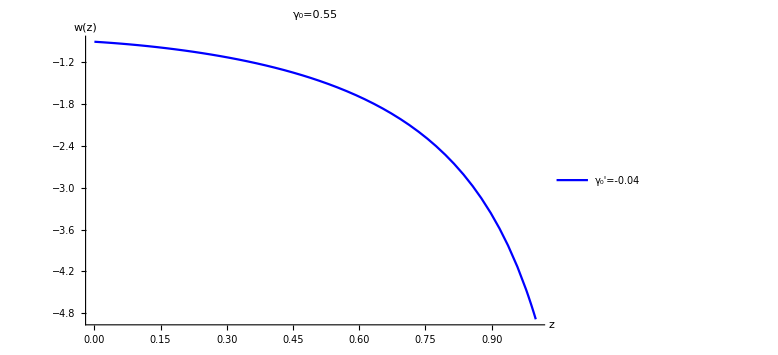

```mathematica
p04n=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=-0.04"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.55", Black, FontSize->20]]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

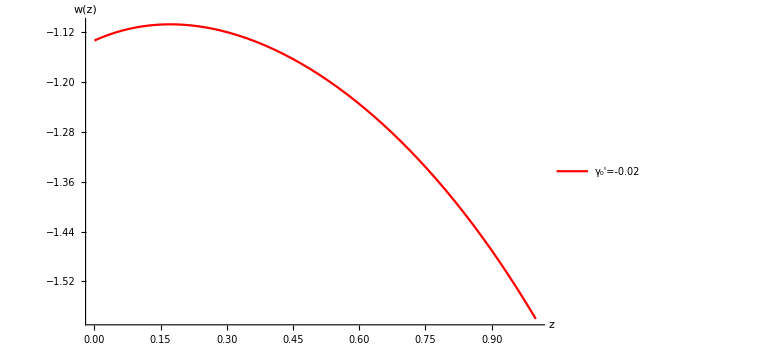

```mathematica
p02n=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=-0.02"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

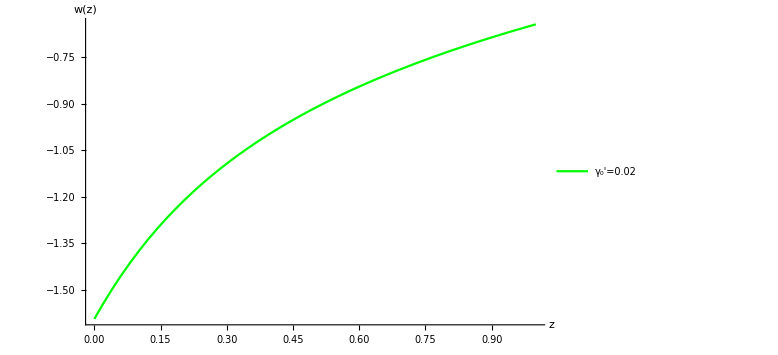

```mathematica
p02=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=0.02"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Green}, ImageSize->Large]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

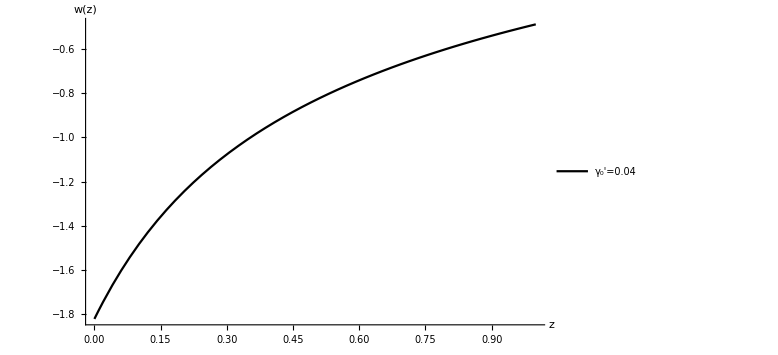

```mathematica
p04=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=0.04"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Black}, ImageSize->Large]
```

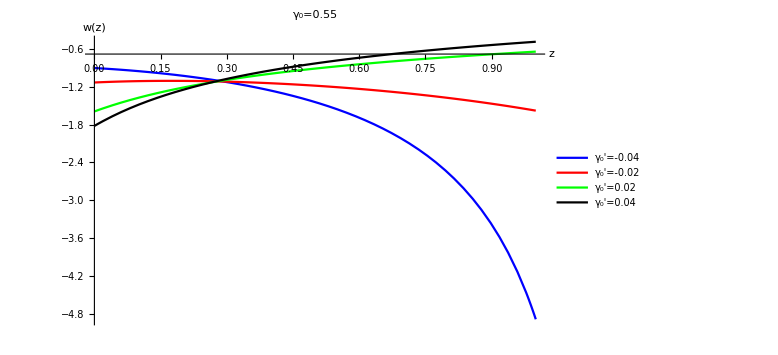

```mathematica
Show[{p04n, p02n, p02, p04}, PlotRange->All]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma053+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gamma053=0.54;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {a,efe[a]} = {0.5,-1.02498×10^-10}.

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

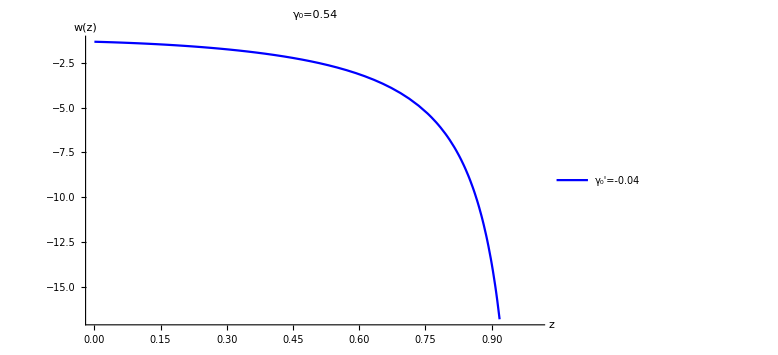

```mathematica
p04n=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=-0.04"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.54", Black, FontSize->20]]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
p02n=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=-0.02"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large]
```

-Graphics-

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
p02=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=0.02"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Green}, ImageSize->Large]
```

-Graphics-

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
p04=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=0.04"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Black}, ImageSize->Large]
```

-Graphics-

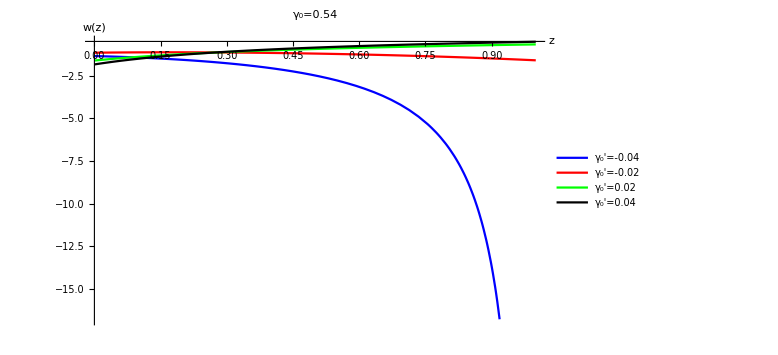

```mathematica
Show[{p04n, p02n, p02, p04}, PlotRange->{0,-5}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma5[a_]=gamma057+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma5[a];
```

```mathematica
om=0.3;
gamma057=0.57;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

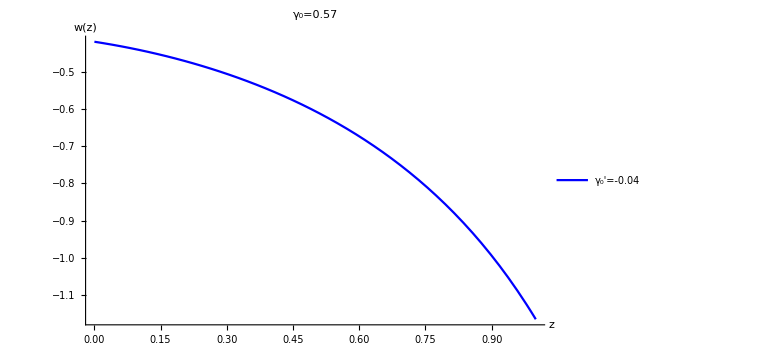

```mathematica
p04n=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=-0.04"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.57", Black, FontSize->20]]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
p02n=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=-0.02"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large]
```

-Graphics-

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
p02=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=0.02"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Green}, ImageSize->Large]
```

-Graphics-

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
p04=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=0.04"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Black}, ImageSize->Large]
```

-Graphics-

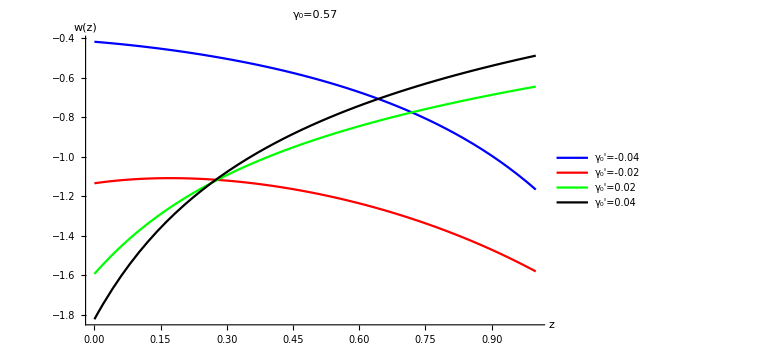

```mathematica
Show[{p04n, p02n, p02, p04}, PlotRange->{0,-5}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma059+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gamma059=0.59;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

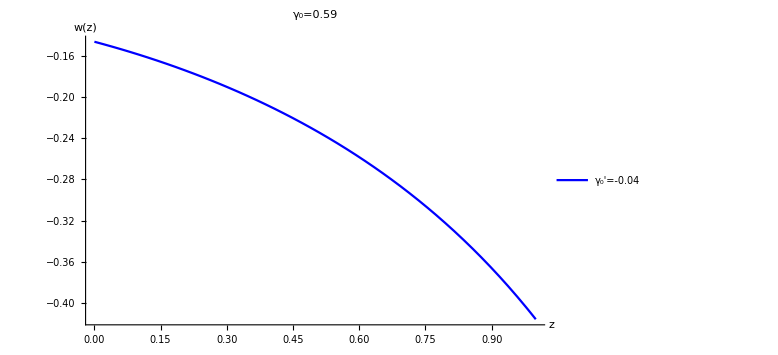

```mathematica
p04n=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=-0.04"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0=0.59", Black, FontSize->20]]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
p02n=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=-0.02"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large]
```

-Graphics-

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
p02=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=0.02"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Green}, ImageSize->Large]
```

-Graphics-

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
p04=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0'=0.04"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Black}, ImageSize->Large]
```

-Graphics-

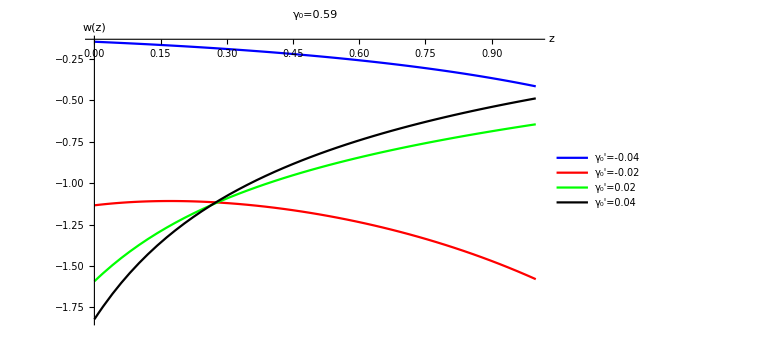

```mathematica
Show[{p04n, p02n, p02, p04}, PlotRange->{0,-5}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma5[a_]=gamma051+gammap001n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma5[a];
```

```mathematica
om=0.3;
gamma051=0.53;
gammap001n=-0.01;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

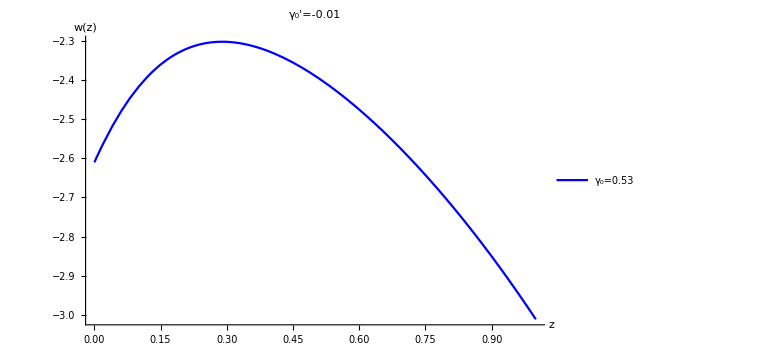

```mathematica
p51=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0=0.53"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Blue}, ImageSize->Large, PlotLabel->Style["γ_0'=-0.01", Black, FontSize->20]]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma6[a_]=gamma054+gammap001n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma6[a];
```

```mathematica
om=0.3;
gamma054=0.54;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

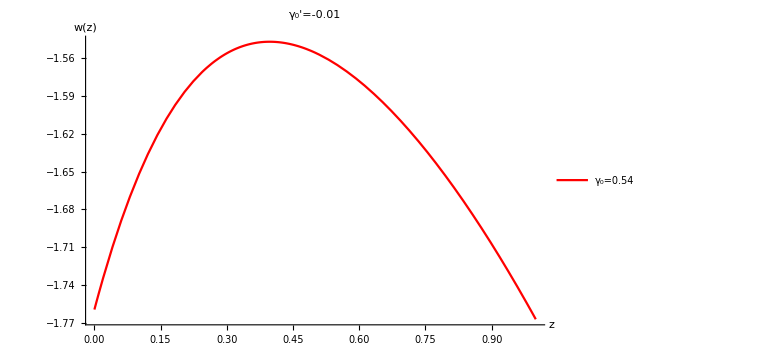

```mathematica
p54=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0=0.54"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Red}, ImageSize->Large, PlotLabel->Style["γ_0'=-0.01", Black, FontSize->20]]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma7[a_]=gamma056+gammap001n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma7[a];
```

```mathematica
om=0.3;
gamma056=0.56;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

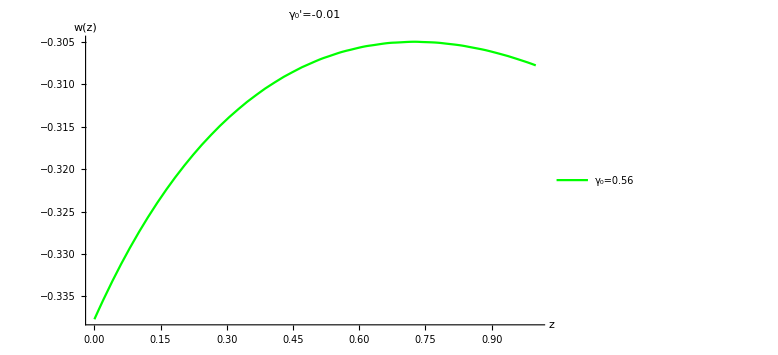

```mathematica
p56=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0=0.56"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Green}, ImageSize->Large, PlotLabel->Style["γ_0'=-0.01", Black, FontSize->20]]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma8[a_]=gamma059+gammap001n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma7[a];
```

```mathematica
om=0.3;
gamma056=0.59;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

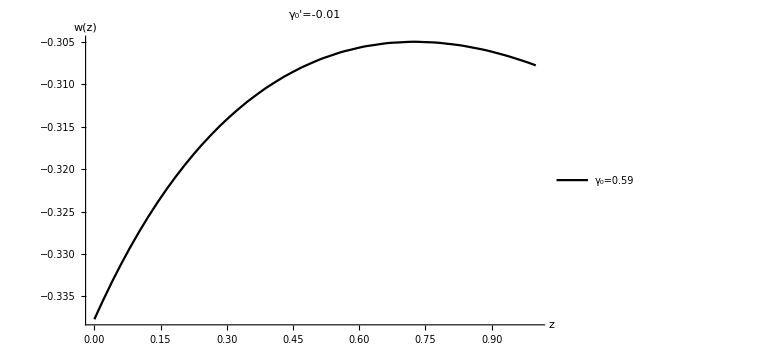

```mathematica
p59=Plot[w[z],{z,0,1}, PlotLegends->{"γ_0=0.59"}, Frame ->False,AxesLabel->{Style["z", Black, FontSize->20],Style["w(z)", Black, FontSize->20]},FrameTicksStyle->Directive["Label", 14, Black], PlotStyle->{Thick, Black}, ImageSize->Large, PlotLabel->Style["γ_0'=-0.01", Black, FontSize->20]]
```